```mathematica
SimulateBiLR[n_]:=Module[{data,cov,sxy,sxx},

data=Table[RandomVariate[MultinormalDistribution[{1,2},{{2,3},{3,5}}]],{n}];

cov=Covariance[data];
sxy=cov[[1]][[2]];
sxx=cov[[2]][[2]];

{sxy,sxx}
]
```

```mathematica
mcSim=Table[SimulateBiLR[100],{500}];
```

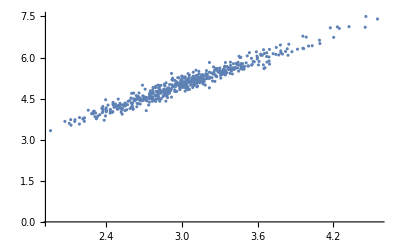

```mathematica
ListPlot[mcSim]
```

```mathematica
Mean[(#[[1]]/#[[2]]&)/@mcSim]
```

0.600007